```mathematica
ColorSSSMatrix[graph_,graphFormat_:FormatGraph,vertices_:Null, sols_]:=Block[{result,bg, sorted,sums},
sorted=Graph[Sort[VertexList[graph]],Sort[EdgeList[graph],EdgeComp]];
sums=Association[];
Table[sums[v]={0,0},{v,VertexList[sorted]}];
result=TableForm[
Table[
bg=None;
Framed[
With[
{
mat=ColorSubMatrix[sols,i,j]
},
sums[i]=sums[i]+mat;
sums[j]=sums[j]+mat;
If[mat[[1]]==0,bg=LightRed];
If[MemberQ[vertices,i]&&MemberQ[vertices,j],bg=LightRed];
If[i==j,bg=LightYellow];
If[EdgeQ[sorted,i<->j],bg=LightBlue];
TableForm[mat]
],
Background->bg
],
{i,VertexList[sorted]},
{j,VertexList[sorted]}],
TableHeadings->{Map[If[MemberQ[vertices,#],Style[#,Bold,Red],#]&,VertexList[sorted]], Map[If[MemberQ[vertices,#],Style[#,Bold,Red],#]&,VertexList[sorted]]},
TableSpacing->{0, 0}
];
{graphFormat[sorted],result,
TableForm[
Map[Framed[{N[#[[1]]/#[[2]]],#[[1]]/#[[2]],TableForm[#]}]&,Values[sums]],
TableHeadings->{Map[If[MemberQ[vertices,#],Style[#,Bold,Red],#]&,Keys[sums]], Map[If[MemberQ[vertices,#],Style[#,Bold,Red],#]&,Keys[sums]]},
TableSpacing->{0, 0}
],
Total[Map[sums[#][[1]]&,Keys[sums]]]/Total[Map[sums[#][[2]]&,Keys[sums]]],
N[Total[Map[sums[#][[1]]&,Keys[sums]]]/Total[Map[sums[#][[2]]&,Keys[sums]]]]
}
]
```

```mathematica
CalcEqual[sols_,v1_,v2_]:=Block[
{couplesols=Map[{Symbol["x"<>ToString[v1]],Symbol["x"<>ToString[v2]]}/.#&,sols]},
Length[Select[couplesols,#[[1]]==#[[2]]&]]
]
```

```mathematica
AlfaBetaPentagon[g_,center_,neighbours_]:=Block[
{ emptyg, sols, sols2,couplesols,f,
alfa,beta,gamma,delta,epsilon, 
alfa1,beta1,gamma1,delta1,epsilon1,
alfa2,beta2,gamma2,delta2,epsilon2,
lambda, full},

PrintTemporary["Solving g.." ];
emptyg=VertexDelete[g,center];
sols=Solve[ToEquations[emptyg],SymbolRange[emptyg]];
full=ChromaticPolynomial[g,4];
PrintTemporary["Solved g" ];
lambda=Length[sols];
alfa=CalcEqual[sols,neighbours[[1]],neighbours[[3]]];
beta=CalcEqual[sols,neighbours[[1]],neighbours[[4]]];
gamma=CalcEqual[sols,neighbours[[2]],neighbours[[4]]];
delta=CalcEqual[sols,neighbours[[2]],neighbours[[5]]];
epsilon=CalcEqual[sols,neighbours[[3]],neighbours[[5]]];

PrintTemporary["Solving g 1/3.." ];
f=VertexContract[emptyg,{neighbours[[1]],neighbours[[3]]}];
sols2=Solve[ToEquations[f],SymbolRange[f]];
gamma2=CalcEqual[sols2,neighbours[[2]],neighbours[[4]]];
delta1=CalcEqual[sols2,neighbours[[2]],neighbours[[5]]];


PrintTemporary["Solving g 1/4.." ];
f=VertexContract[emptyg,{neighbours[[1]],neighbours[[4]]}];
sols2=Solve[ToEquations[f],SymbolRange[f]];
delta2=CalcEqual[sols2,neighbours[[2]],neighbours[[5]]];
epsilon1=CalcEqual[sols2,neighbours[[3]],neighbours[[5]]];

PrintTemporary["Solving g 2/4.." ];
f=VertexContract[emptyg,{neighbours[[2]],neighbours[[4]]}];
sols2=Solve[ToEquations[f],SymbolRange[f]];
alfa1=CalcEqual[sols2,neighbours[[1]],neighbours[[3]]];
epsilon2=CalcEqual[sols2,neighbours[[3]],neighbours[[5]]];

PrintTemporary["Solving g 2/5.." ];
f=VertexContract[emptyg,{neighbours[[2]],neighbours[[5]]}];
sols2=Solve[ToEquations[f],SymbolRange[f]];
alfa2=CalcEqual[sols2,neighbours[[1]],neighbours[[3]]];
beta1=CalcEqual[sols2,neighbours[[1]],neighbours[[4]]];

PrintTemporary["Solving g 3/5.." ];
f=VertexContract[emptyg,{neighbours[[3]],neighbours[[5]]}];
sols2=Solve[ToEquations[f],SymbolRange[f]];
beta2=CalcEqual[sols2,neighbours[[1]],neighbours[[4]]];
gamma1=CalcEqual[sols2,neighbours[[2]],neighbours[[4]]];

Column[{
TableForm[
Map[{#}&,{lambda/24,full/24,Style[alfa/24,Red],alfa1/24,alfa2/24,Style[beta/24,Red],beta1/24,beta2/24,Style[gamma/24,Red],gamma1/24,gamma2/24,Style[delta/24,Red],delta1/24,delta2/24,Style[epsilon/24,Red],epsilon1/24,epsilon2/24,(alfa+beta+gamma+delta+epsilon)/24}],
TableHeadings->{{λ,Σ,α,α1,α2,β,β1,β2,γ,γ1,γ2,δ,δ1,δ2,ϵ,ϵ1,ϵ2,α+β+γ+δ+ϵ},None},
TableDirections->Row,
TableAlignments->Center,
TableSpacing->{1, 1}
],
ColorSSSMatrix[VertexDelete[g,center],Graph[#,GraphLayout->"TutteEmbedding", VertexLabels->"Name"]&,neighbours,sols]
}
]
]
```

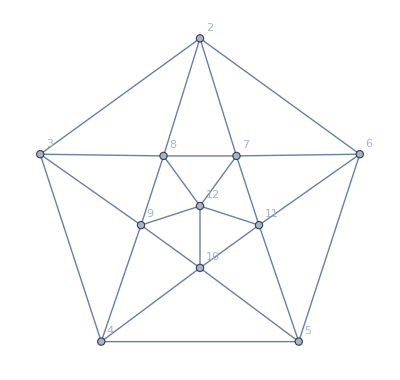
λ | Σ | α | α1 | α2 | β | β1 | β2 | γ | γ1 | γ2 | δ | δ1 | δ2 | ϵ | ϵ1 | ϵ2 | α+β+γ+δ+ϵ
20 | 10 | 6 | 2 | 2 | 6 | 2 | 2 | 6 | 2 | 2 | 6 | 2 | 2 | 6 | 2 | 2 | 30
{-Graphics-, | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 20
0 | 0
20 | 6
14 | 6
14 | 0
20 | 0
20 | 0
20 | 9
11 | 1
19 | 9
11 | 7
13
3 | 0
20 | 20
0 | 0
20 | 6
14 | 6
14 | 9
11 | 0
20 | 0
20 | 9
11 | 1
19 | 7
13
4 | 6
14 | 0
20 | 20
0 | 0
20 | 6
14 | 1
19 | 9
11 | 0
20 | 0
20 | 9
11 | 7
13
5 | 6
14 | 6
14 | 0
20 | 20
0 | 0
20 | 9
11 | 1
19 | 9
11 | 0
20 | 0
20 | 7
13
6 | 0
20 | 6
14 | 6
14 | 0
20 | 20
0 | 0
20 | 9
11 | 1
19 | 9
11 | 0
20 | 7
13
7 | 0
20 | 9
11 | 1
19 | 9
11 | 0
20 | 20
0 | 0
20 | 8
12 | 8
12 | 0
20 | 0
20
8 | 0
20 | 0
20 | 9
11 | 1
19 | 9
11 | 0
20 | 20
0 | 0
20 | 8
12 | 8
12 | 0
20
9 | 9
11 | 0
20 | 0
20 | 9
11 | 1
19 | 8
12 | 0
20 | 20
0 | 0
20 | 8
12 | 0
20
10 | 1
19 | 9
11 | 0
20 | 0
20 | 9
11 | 8
12 | 8
12 | 0
20 | 20
0 | 0
20 | 0
20
11 | 9
11 | 1
19 | 9
11 | 0
20 | 0
20 | 0
20 | 8
12 | 8
12 | 0
20 | 20
0 | 0
20
12 | 7
13 | 7
13 | 7
13 | 7
13 | 7
13 | 0
20 | 0
20 | 0
20 | 0
20 | 0
20 | 20
0,2 | {0.358025,29/81,116
324}
3 | {0.358025,29/81,116
324}
4 | {0.358025,29/81,116
324}
5 | {0.358025,29/81,116
324}
6 | {0.358025,29/81,116
324}
7 | {0.333333,1/3,110
330}
8 | {0.333333,1/3,110
330}
9 | {0.333333,1/3,110
330}
10 | {0.333333,1/3,110
330}
11 | {0.333333,1/3,110
330}
12 | {0.333333,1/3,110
330},31/90,0.344444}

```mathematica
AlfaBetaPentagon[Graph[plantri[[1]]],1,{2,3,4,5,6}]
```

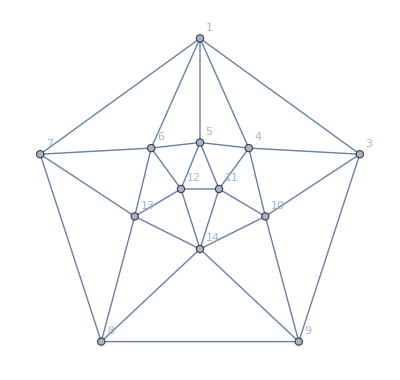
λ | Σ | α | α1 | α2 | β | β1 | β2 | γ | γ1 | γ2 | δ | δ1 | δ2 | ϵ | ϵ1 | ϵ2 | α+β+γ+δ+ϵ
40 | 20 | 13 | 3 | 6 | 13 | 6 | 3 | 8 | 2 | 3 | 18 | 6 | 6 | 8 | 3 | 2 | 60
{-Graphics-, | 1 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
1 | 40
0 | 0
40 | 0
40 | 0
40 | 0
40 | 0
40 | 13
27 | 13
27 | 21
19 | 17
23 | 17
23 | 21
19 | 1
39
3 | 0
40 | 40
0 | 0
40 | 23
17 | 12
28 | 18
22 | 8
32 | 0
40 | 0
40 | 11
29 | 2
38 | 4
36 | 22
18
4 | 0
40 | 0
40 | 40
0 | 0
40 | 16
24 | 12
28 | 6
34 | 16
24 | 0
40 | 0
40 | 15
25 | 5
35 | 12
28
5 | 0
40 | 23
17 | 0
40 | 40
0 | 0
40 | 23
17 | 4
36 | 4
36 | 8
32 | 0
40 | 0
40 | 8
32 | 23
17
6 | 0
40 | 12
28 | 16
24 | 0
40 | 40
0 | 0
40 | 16
24 | 6
34 | 5
35 | 15
25 | 0
40 | 0
40 | 12
28
7 | 0
40 | 18
22 | 12
28 | 23
17 | 0
40 | 40
0 | 0
40 | 8
32 | 4
36 | 2
38 | 11
29 | 0
40 | 22
18
8 | 13
27 | 8
32 | 6
34 | 4
36 | 16
24 | 0
40 | 40
0 | 0
40 | 22
18 | 10
30 | 19
21 | 0
40 | 0
40
9 | 13
27 | 0
40 | 16
24 | 4
36 | 6
34 | 8
32 | 0
40 | 40
0 | 0
40 | 19
21 | 10
30 | 22
18 | 0
40
10 | 21
19 | 0
40 | 0
40 | 8
32 | 5
35 | 4
36 | 22
18 | 0
40 | 40
0 | 0
40 | 22
18 | 8
32 | 0
40
11 | 17
23 | 11
29 | 0
40 | 0
40 | 15
25 | 2
38 | 10
30 | 19
21 | 0
40 | 40
0 | 0
40 | 22
18 | 0
40
12 | 17
23 | 2
38 | 15
25 | 0
40 | 0
40 | 11
29 | 19
21 | 10
30 | 22
18 | 0
40 | 40
0 | 0
40 | 0
40
13 | 21
19 | 4
36 | 5
35 | 8
32 | 0
40 | 0
40 | 0
40 | 22
18 | 8
32 | 22
18 | 0
40 | 40
0 | 0
40
14 | 1
39 | 22
18 | 12
28 | 23
17 | 12
28 | 22
18 | 0
40 | 0
40 | 0
40 | 0
40 | 0
40 | 0
40 | 40
0,1 | {0.37931,11/29,286
754}
3 | {0.368421,7/19,280
760}
4 | {0.306533,61/199,244
796}
5 | {0.343669,133/387,266
774}
6 | {0.306533,61/199,244
796}
7 | {0.368421,7/19,280
760}
8 | {0.361257,69/191,276
764}
9 | {0.361257,69/191,276
764}
10 | {0.333333,1/3,260
780}
11 | {0.354167,17/48,272
768}
12 | {0.354167,17/48,272
768}
13 | {0.333333,1/3,260
780}
14 | {0.340206,33/97,264
776},87/251,0.346614}

```mathematica
AlfaBetaPentagon[Graph[plantri[[2]]],2,{1,3,9,8,7}]
```

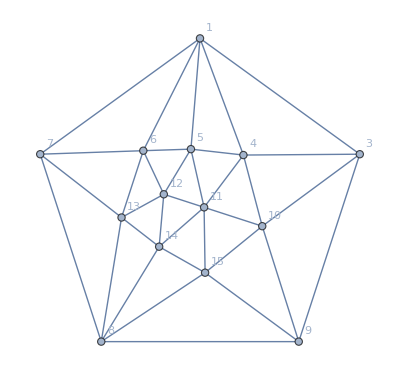
λ | Σ | α | α1 | α2 | β | β1 | β2 | γ | γ1 | γ2 | δ | δ1 | δ2 | ϵ | ϵ1 | ϵ2 | α+β+γ+δ+ϵ
48 | 32 | 18 | 8 | 6 | 16 | 6 | 6 | 18 | 6 | 8 | 14 | 6 | 6 | 14 | 6 | 6 | 80
{-Graphics-, | 1 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
1 | 48
0 | 0
48 | 0
48 | 0
48 | 0
48 | 0
48 | 16
32 | 18
30 | 21
27 | 19
29 | 19
29 | 22
26 | 4
44 | 4
44
3 | 0
48 | 48
0 | 0
48 | 19
29 | 20
28 | 14
34 | 18
30 | 0
48 | 0
48 | 19
29 | 6
42 | 10
38 | 6
42 | 19
29
4 | 0
48 | 0
48 | 48
0 | 0
48 | 18
30 | 18
30 | 4
44 | 19
29 | 0
48 | 0
48 | 19
29 | 5
43 | 18
30 | 20
28
5 | 0
48 | 19
29 | 0
48 | 48
0 | 0
48 | 22
26 | 4
44 | 6
42 | 18
30 | 0
48 | 0
48 | 16
32 | 22
26 | 18
30
6 | 0
48 | 20
28 | 18
30 | 0
48 | 48
0 | 0
48 | 22
26 | 10
38 | 5
43 | 21
27 | 0
48 | 0
48 | 16
32 | 5
43
7 | 0
48 | 14
34 | 18
30 | 22
26 | 0
48 | 48
0 | 0
48 | 14
34 | 9
39 | 3
45 | 17
31 | 0
48 | 22
26 | 18
30
8 | 16
32 | 18
30 | 4
44 | 4
44 | 22
26 | 0
48 | 48
0 | 0
48 | 21
27 | 19
29 | 19
29 | 0
48 | 0
48 | 0
48
9 | 18
30 | 0
48 | 19
29 | 6
42 | 10
38 | 14
34 | 0
48 | 48
0 | 0
48 | 19
29 | 6
42 | 20
28 | 19
29 | 0
48
10 | 21
27 | 0
48 | 0
48 | 18
30 | 5
43 | 9
39 | 21
27 | 0
48 | 48
0 | 0
48 | 20
28 | 5
43 | 18
30 | 0
48
11 | 19
29 | 19
29 | 0
48 | 0
48 | 21
27 | 3
45 | 19
29 | 19
29 | 0
48 | 48
0 | 0
48 | 21
27 | 0
48 | 0
48
12 | 19
29 | 6
42 | 19
29 | 0
48 | 0
48 | 17
31 | 19
29 | 6
42 | 20
28 | 0
48 | 48
0 | 0
48 | 0
48 | 19
29
13 | 22
26 | 10
38 | 5
43 | 16
32 | 0
48 | 0
48 | 0
48 | 20
28 | 5
43 | 21
27 | 0
48 | 48
0 | 0
48 | 18
30
14 | 4
44 | 6
42 | 18
30 | 22
26 | 16
32 | 22
26 | 0
48 | 19
29 | 18
30 | 0
48 | 0
48 | 0
48 | 48
0 | 0
48
15 | 4
44 | 19
29 | 20
28 | 18
30 | 5
43 | 18
30 | 0
48 | 0
48 | 0
48 | 0
48 | 19
29 | 18
30 | 0
48 | 48
0,1 | {0.341317,57/167,342
1002}
3 | {0.363083,179/493,358
986}
4 | {0.335984,169/503,338
1006}
5 | {0.346693,173/499,346
998}
6 | {0.325444,55/169,330
1014}
7 | {0.379877,185/487,370
974}
8 | {0.341317,57/167,342
1002}
9 | {0.363083,179/493,358
986}
10 | {0.325444,55/169,330
1014}
11 | {0.335984,169/503,338
1006}
12 | {0.346693,173/499,346
998}
13 | {0.325444,55/169,330
1014}
14 | {0.346693,173/499,346
998}
15 | {0.335984,169/503,338
1006},401/1167,0.343616}

```mathematica
AlfaBetaPentagon[Graph[plantri[[3]]],2,{1,3,9,8,7}]
```

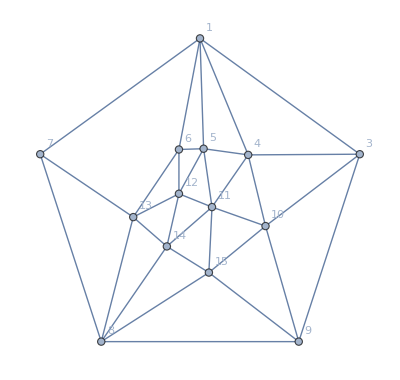
λ | Σ | α | α1 | α2 | β | β1 | β2 | γ | γ1 | γ2 | δ | δ1 | δ2 | ϵ | ϵ1 | ϵ2 | α+β+γ+δ+ϵ
82 | 48 | 28 | 10 | 8 | 32 | 8 | 14 | 22 | 8 | 10 | 18 | 8 | 8 | 30 | 14 | 8 | 130
{-Graphics-, | 1 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
1 | 82
0 | 0
82 | 0
82 | 0
82 | 0
82 | 0
82 | 32
50 | 28
54 | 37
45 | 35
47 | 36
46 | 32
50 | 5
77 | 6
76
3 | 0
82 | 82
0 | 0
82 | 39
43 | 24
58 | 18
64 | 22
60 | 0
82 | 0
82 | 27
55 | 10
72 | 24
58 | 10
72 | 39
43
4 | 0
82 | 0
82 | 82
0 | 0
82 | 40
42 | 40
42 | 8
74 | 35
47 | 0
82 | 0
82 | 26
56 | 7
75 | 39
43 | 28
54
5 | 0
82 | 39
43 | 0
82 | 82
0 | 0
82 | 22
60 | 9
73 | 8
74 | 26
56 | 0
82 | 0
82 | 32
50 | 29
53 | 38
44
6 | 0
82 | 24
58 | 40
42 | 0
82 | 82
0 | 34
48 | 22
60 | 26
56 | 9
73 | 27
55 | 0
82 | 0
82 | 39
43 | 10
72
7 | 0
82 | 18
64 | 40
42 | 22
60 | 34
48 | 82
0 | 0
82 | 30
52 | 13
69 | 9
73 | 17
65 | 0
82 | 45
37 | 23
59
8 | 32
50 | 22
60 | 8
74 | 9
73 | 22
60 | 0
82 | 82
0 | 0
82 | 43
39 | 25
57 | 42
40 | 0
82 | 0
82 | 0
82
9 | 28
54 | 0
82 | 35
47 | 8
74 | 26
56 | 30
52 | 0
82 | 82
0 | 0
82 | 35
47 | 7
75 | 30
52 | 36
46 | 0
82
10 | 37
45 | 0
82 | 0
82 | 26
56 | 9
73 | 13
69 | 43
39 | 0
82 | 82
0 | 0
82 | 41
41 | 7
75 | 25
57 | 0
82
11 | 35
47 | 27
55 | 0
82 | 0
82 | 27
55 | 9
73 | 25
57 | 35
47 | 0
82 | 82
0 | 0
82 | 37
45 | 0
82 | 0
82
12 | 36
46 | 10
72 | 26
56 | 0
82 | 0
82 | 17
65 | 42
40 | 7
75 | 41
41 | 0
82 | 82
0 | 0
82 | 0
82 | 26
56
13 | 32
50 | 24
58 | 7
75 | 32
50 | 0
82 | 0
82 | 0
82 | 30
52 | 7
75 | 37
45 | 0
82 | 82
0 | 0
82 | 34
48
14 | 5
77 | 10
72 | 39
43 | 29
53 | 39
43 | 45
37 | 0
82 | 36
46 | 25
57 | 0
82 | 0
82 | 0
82 | 82
0 | 0
82
15 | 6
76 | 39
43 | 28
54 | 38
44 | 10
72 | 23
59 | 0
82 | 0
82 | 0
82 | 0
82 | 26
56 | 34
48 | 0
82 | 82
0}

```mathematica
AlfaBetaPentagon[EdgeDelete[Graph[plantri[[3]]],7<->6],2,{1,3,9,8,7}]
```

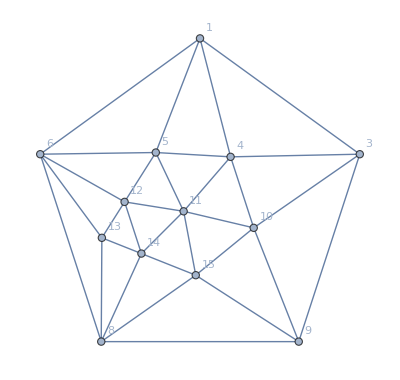
λ | Σ | α | α1 | α2 | β | β1 | β2 | γ | γ1 | γ2 | δ | δ1 | δ2 | ϵ | ϵ1 | ϵ2 | α+β+γ+δ+ϵ
34 | 16 | 10 | 2 | 2 | 16 | 2 | 8 | 4 | 2 | 2 | 4 | 2 | 2 | 16 | 8 | 2 | 50
{-Graphics-, | 1 | 3 | 4 | 5 | 6 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
1 | 34
0 | 0
34 | 0
34 | 0
34 | 0
34 | 16
18 | 10
24 | 16
18 | 16
18 | 17
17 | 10
24 | 1
33 | 2
32
3 | 0
34 | 34
0 | 0
34 | 20
14 | 4
30 | 4
30 | 0
34 | 0
34 | 8
26 | 4
30 | 14
20 | 4
30 | 20
14
4 | 0
34 | 0
34 | 34
0 | 0
34 | 22
12 | 4
30 | 16
18 | 0
34 | 0
34 | 7
27 | 2
32 | 21
13 | 8
26
5 | 0
34 | 20
14 | 0
34 | 34
0 | 0
34 | 5
29 | 2
32 | 8
26 | 0
34 | 0
34 | 16
18 | 7
27 | 20
14
6 | 0
34 | 4
30 | 22
12 | 0
34 | 34
0 | 0
34 | 16
18 | 4
30 | 6
28 | 0
34 | 0
34 | 23
11 | 5
29
8 | 16
18 | 4
30 | 4
30 | 5
29 | 0
34 | 34
0 | 0
34 | 22
12 | 6
28 | 23
11 | 0
34 | 0
34 | 0
34
9 | 10
24 | 0
34 | 16
18 | 2
32 | 16
18 | 0
34 | 34
0 | 0
34 | 16
18 | 1
33 | 10
24 | 17
17 | 0
34
10 | 16
18 | 0
34 | 0
34 | 8
26 | 4
30 | 22
12 | 0
34 | 34
0 | 0
34 | 21
13 | 2
32 | 7
27 | 0
34
11 | 16
18 | 8
26 | 0
34 | 0
34 | 6
28 | 6
28 | 16
18 | 0
34 | 34
0 | 0
34 | 16
18 | 0
34 | 0
34
12 | 17
17 | 4
30 | 7
27 | 0
34 | 0
34 | 23
11 | 1
33 | 21
13 | 0
34 | 34
0 | 0
34 | 0
34 | 7
27
13 | 10
24 | 14
20 | 2
32 | 16
18 | 0
34 | 0
34 | 10
24 | 2
32 | 16
18 | 0
34 | 34
0 | 0
34 | 16
18
14 | 1
33 | 4
30 | 21
13 | 7
27 | 23
11 | 0
34 | 17
17 | 7
27 | 0
34 | 0
34 | 0
34 | 34
0 | 0
34
15 | 2
32 | 20
14 | 8
26 | 20
14 | 5
29 | 0
34 | 0
34 | 0
34 | 0
34 | 7
27 | 16
18 | 0
34 | 34
0}

```mathematica
AlfaBetaPentagon[EdgeContract[Graph[plantri[[3]]],7<->6],2,{1,3,9,8,6}]
```

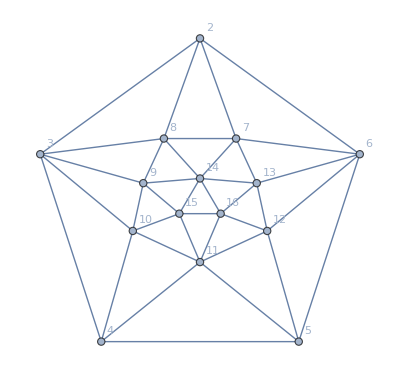
λ | Σ | α | α1 | α2 | β | β1 | β2 | γ | γ1 | γ2 | δ | δ1 | δ2 | ϵ | ϵ1 | ϵ2 | α+β+γ+δ+ϵ
60 | 30 | 14 | 2 | 10 | 14 | 10 | 2 | 14 | 6 | 2 | 34 | 10 | 10 | 14 | 2 | 6 | 90
{-Graphics-, | 2 | 6 | 5 | 4 | 3
2 | 60
0 | 0
60 | 14
46 | 14
46 | 0
60
6 | 0
60 | 60
0 | 0
60 | 14
46 | 34
26
5 | 14
46 | 0
60 | 60
0 | 0
60 | 14
46
4 | 14
46 | 14
46 | 0
60 | 60
0 | 0
60
3 | 0
60 | 34
26 | 14
46 | 0
60 | 60
0}

```mathematica
AlfaBetaPentagon[Graph[plantri[[4]]],1,{2,6,5,4,3}]
```

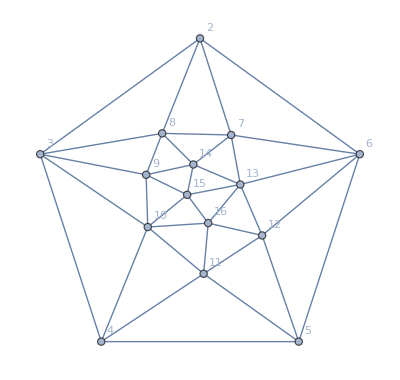
λ | Σ | α | α1 | α2 | β | β1 | β2 | γ | γ1 | γ2 | δ | δ1 | δ2 | ϵ | ϵ1 | ϵ2 | α+β+γ+δ+ϵ
58 | 27 | 14 | 8 | 2 | 20 | 7 | 4 | 25 | 6 | 8 | 14 | 2 | 7 | 12 | 4 | 6 | 85
{-Graphics-, | 4 | 3 | 2 | 6 | 5
4 | 58
0 | 0
58 | 14
44 | 20
38 | 0
58
3 | 0
58 | 58
0 | 0
58 | 25
33 | 14
44
2 | 14
44 | 0
58 | 58
0 | 0
58 | 12
46
6 | 20
38 | 25
33 | 0
58 | 58
0 | 0
58
5 | 0
58 | 14
44 | 12
46 | 0
58 | 58
0}

$Aborted

```mathematica
AlfaBetaPentagon[Graph[plantri[[5]]],1,{4,3,2,6,5}]
```

```mathematica
g=VertexDelete[Graph[plantri[[24534]]],{14,15,22,20,19,18,24,17,16,23,25}];MaximalPlanarQ[g]
```

True

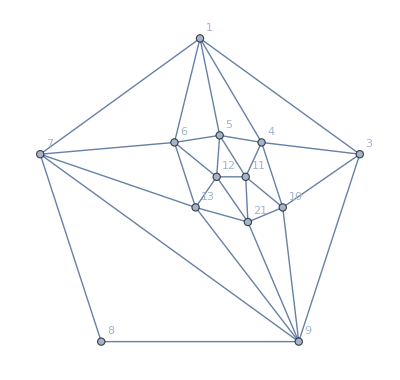
λ | Σ | α | α1 | α2 | β | β1 | β2 | γ | γ1 | γ2 | δ | δ1 | δ2 | ϵ | ϵ1 | ϵ2 | α+β+γ+δ+ϵ
36 | 14 | 12 | 4 | 4 | 12 | 6 | 8 | 10 | 8 | 4 | 16 | 4 | 6 | 0 | 0 | 0 | 50
{-Graphics-, | 1 | 3 | 9 | 8 | 7
1 | 36
0 | 0
36 | 12
24 | 12
24 | 0
36
3 | 0
36 | 36
0 | 0
36 | 10
26 | 16
20
9 | 12
24 | 0
36 | 36
0 | 0
36 | 0
36
8 | 12
24 | 10
26 | 0
36 | 36
0 | 0
36
7 | 0
36 | 16
20 | 0
36 | 0
36 | 36
0}

```mathematica
AlfaBetaPentagon[g,2,{1,3,9,8,7}]
```

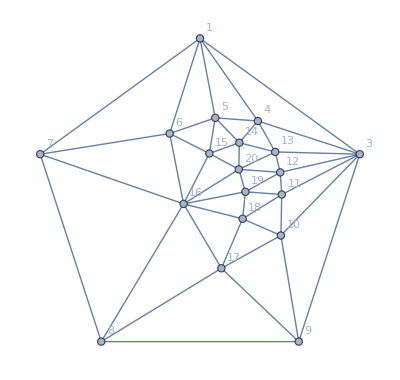
λ | Σ | α | α1 | α2 | β | β1 | β2 | γ | γ1 | γ2 | δ | δ1 | δ2 | ϵ | ϵ1 | ϵ2 | α+β+γ+δ+ϵ
192 | 108 | 77 | 27 | 30 | 45 | 22 | 11 | 64 | 18 | 27 | 74 | 30 | 22 | 40 | 11 | 18 | 300
{-Graphics-, | 1 | 3 | 9 | 8 | 7
1 | 192
0 | 0
192 | 77
115 | 45
147 | 0
192
3 | 0
192 | 192
0 | 0
192 | 64
128 | 74
118
9 | 77
115 | 0
192 | 192
0 | 0
192 | 40
152
8 | 45
147 | 64
128 | 0
192 | 192
0 | 0
192
7 | 0
192 | 74
118 | 40
152 | 0
192 | 192
0}

```mathematica
AlfaBetaPentagon[Graph[plantri[[100]]],2,{1,3,9,8,7}]
```

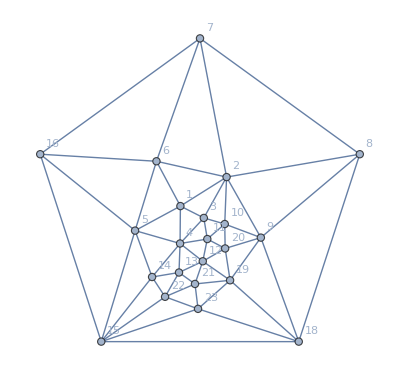
λ | Σ | α | α1 | α2 | β | β1 | β2 | γ | γ1 | γ2 | δ | δ1 | δ2 | ϵ | ϵ1 | ϵ2 | α+β+γ+δ+ϵ
416 | 224 | 91 | 48 | 22 | 92 | 23 | 47 | 191 | 84 | 48 | 78 | 22 | 23 | 188 | 47 | 84 | 640
{-Graphics-, | 7 | 8 | 18 | 15 | 16
7 | 416
0 | 0
416 | 91
325 | 92
324 | 0
416
8 | 0
416 | 416
0 | 0
416 | 191
225 | 78
338
18 | 91
325 | 0
416 | 416
0 | 0
416 | 188
228
15 | 92
324 | 191
225 | 0
416 | 416
0 | 0
416
16 | 0
416 | 78
338 | 188
228 | 0
416 | 416
0}

```mathematica
AlfaBetaPentagon[Graph[plantri[[1000]]],17,{7,8,18,15,16}]
```

```mathematica
AlfaBetaPentagon[Graph[plantri[[10000]]],1,{2,6,5,4,3}]
```

```mathematica
ChromaticPolynomial[Graph[plantri[[1000]]],4]
```

$Aborted

```mathematica
VertexCount[Graph[plantri[[100]]]]
```

20

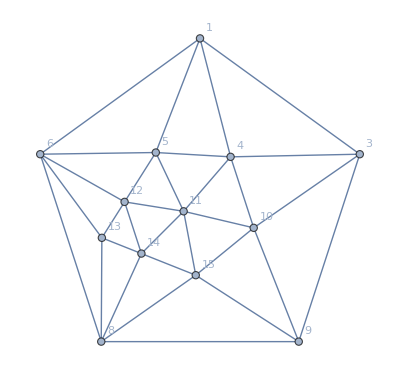

```mathematica
g=Graph[VertexDelete[Graph[{1<->2,1<->3,1<->4,1<->5,2<->8,2<->9,2<->3,3<->9,3<->10,3<->4,4<->10,4<->11,4<->5,5<->11,5<->12,8<->13,8<->14,8<->15,8<->9,9<->15,9<->10,10<->15,10<->11,11<->15,11<->14,11<->12,12<->14,12<->13,13<->14,14<->15,6<->1,6<->2,6<->5,6<->8,6<->12,6<->13}],{2}],GraphLayout->"TutteEmbedding", VertexLabels->"Name"]
```

```mathematica
IsomorphicGraphQ[g,Graph[plantri[[1]]]]
```

False

```mathematica
AlfaBetaPentagon33333[g_,center_,neighbours_]:=Block[
{ emptyg, sols, sols2,couplesols,f,
alfa,beta,gamma,delta,epsilon, 
alfa1,beta1,gamma1,delta1,epsilon1,
alfa2,beta2,gamma2,delta2,epsilon2,
lambda, full},

PrintTemporary["Solving g.." ];
emptyg=g;
sols=Solve[ToEquations[emptyg],SymbolRange[emptyg]];
full=ChromaticPolynomial[g,4];
PrintTemporary["Solved g" ];
lambda=Length[sols];
alfa=CalcEqual[sols,neighbours[[1]],neighbours[[3]]];
beta=CalcEqual[sols,neighbours[[1]],neighbours[[4]]];
gamma=CalcEqual[sols,neighbours[[2]],neighbours[[4]]];
delta=CalcEqual[sols,neighbours[[2]],neighbours[[5]]];
epsilon=CalcEqual[sols,neighbours[[3]],neighbours[[5]]];

PrintTemporary["Solving g 1/3.." ];
f=VertexContract[emptyg,{neighbours[[1]],neighbours[[3]]}];
sols2=Solve[ToEquations[f],SymbolRange[f]];
gamma2=CalcEqual[sols2,neighbours[[2]],neighbours[[4]]];
delta1=CalcEqual[sols2,neighbours[[2]],neighbours[[5]]];


PrintTemporary["Solving g 1/4.." ];
f=VertexContract[emptyg,{neighbours[[1]],neighbours[[4]]}];
sols2=Solve[ToEquations[f],SymbolRange[f]];
delta2=CalcEqual[sols2,neighbours[[2]],neighbours[[5]]];
epsilon1=CalcEqual[sols2,neighbours[[3]],neighbours[[5]]];

PrintTemporary["Solving g 2/4.." ];
f=VertexContract[emptyg,{neighbours[[2]],neighbours[[4]]}];
sols2=Solve[ToEquations[f],SymbolRange[f]];
alfa1=CalcEqual[sols2,neighbours[[1]],neighbours[[3]]];
epsilon2=CalcEqual[sols2,neighbours[[3]],neighbours[[5]]];

PrintTemporary["Solving g 2/5.." ];
f=VertexContract[emptyg,{neighbours[[2]],neighbours[[5]]}];
sols2=Solve[ToEquations[f],SymbolRange[f]];
alfa2=CalcEqual[sols2,neighbours[[1]],neighbours[[3]]];
beta1=CalcEqual[sols2,neighbours[[1]],neighbours[[4]]];

PrintTemporary["Solving g 3/5.." ];
f=VertexContract[emptyg,{neighbours[[3]],neighbours[[5]]}];
sols2=Solve[ToEquations[f],SymbolRange[f]];
beta2=CalcEqual[sols2,neighbours[[1]],neighbours[[4]]];
gamma1=CalcEqual[sols2,neighbours[[2]],neighbours[[4]]];

Column[{
TableForm[
Map[{#}&,{lambda/24,full/24,Style[alfa/24,Red],alfa1/24,alfa2/24,Style[beta/24,Red],beta1/24,beta2/24,Style[gamma/24,Red],gamma1/24,gamma2/24,Style[delta/24,Red],delta1/24,delta2/24,Style[epsilon/24,Red],epsilon1/24,epsilon2/24,(alfa+beta+gamma+delta+epsilon)/24}],
TableHeadings->{{λ,Σ,α,α1,α2,β,β1,β2,γ,γ1,γ2,δ,δ1,δ2,ϵ,ϵ1,ϵ2,α+β+γ+δ+ϵ},None},
TableDirections->Row,
TableAlignments->Center,
TableSpacing->{1, 1}
],
ColorSSSMatrix[g,Graph[#,GraphLayout->"TutteEmbedding", VertexLabels->"Name"]&,neighbours,sols]
}
]
]
```

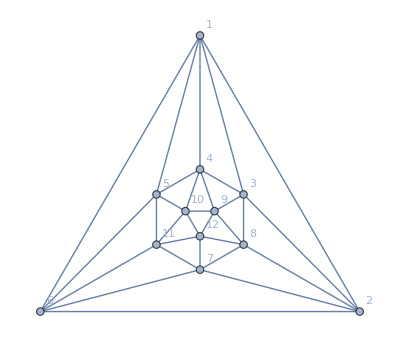
λ | Σ | α | α1 | α2 | β | β1 | β2 | γ | γ1 | γ2 | δ | δ1 | δ2 | ϵ | ϵ1 | ϵ2 | α+β+γ+δ+ϵ
10 | 10 | 4 | 2 | 2 | 4 | 2 | 2 | 4 | 2 | 2 | 4 | 2 | 2 | 4 | 2 | 2 | 20
{-Graphics-, | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
1 | 10
0 | 0
10 | 0
10 | 0
10 | 0
10 | 0
10 | 4
6 | 4
6 | 4
6 | 4
6 | 4
6 | 0
10
2 | 0
10 | 10
0 | 0
10 | 4
6 | 4
6 | 0
10 | 0
10 | 0
10 | 4
6 | 0
10 | 4
6 | 4
6
3 | 0
10 | 0
10 | 10
0 | 0
10 | 4
6 | 4
6 | 4
6 | 0
10 | 0
10 | 4
6 | 0
10 | 4
6
4 | 0
10 | 4
6 | 0
10 | 10
0 | 0
10 | 4
6 | 0
10 | 4
6 | 0
10 | 0
10 | 4
6 | 4
6
5 | 0
10 | 4
6 | 4
6 | 0
10 | 10
0 | 0
10 | 4
6 | 0
10 | 4
6 | 0
10 | 0
10 | 4
6
6 | 0
10 | 0
10 | 4
6 | 4
6 | 0
10 | 10
0 | 0
10 | 4
6 | 0
10 | 4
6 | 0
10 | 4
6
7 | 4
6 | 0
10 | 4
6 | 0
10 | 4
6 | 0
10 | 10
0 | 0
10 | 4
6 | 4
6 | 0
10 | 0
10
8 | 4
6 | 0
10 | 0
10 | 4
6 | 0
10 | 4
6 | 0
10 | 10
0 | 0
10 | 4
6 | 4
6 | 0
10
9 | 4
6 | 4
6 | 0
10 | 0
10 | 4
6 | 0
10 | 4
6 | 0
10 | 10
0 | 0
10 | 4
6 | 0
10
10 | 4
6 | 0
10 | 4
6 | 0
10 | 0
10 | 4
6 | 4
6 | 4
6 | 0
10 | 10
0 | 0
10 | 0
10
11 | 4
6 | 4
6 | 0
10 | 4
6 | 0
10 | 0
10 | 0
10 | 4
6 | 4
6 | 0
10 | 10
0 | 0
10
12 | 0
10 | 4
6 | 4
6 | 4
6 | 4
6 | 4
6 | 0
10 | 0
10 | 0
10 | 0
10 | 0
10 | 10
0,1 | {0.333333,1/3,60
180}
2 | {0.333333,1/3,60
180}
3 | {0.333333,1/3,60
180}
4 | {0.333333,1/3,60
180}
5 | {0.333333,1/3,60
180}
6 | {0.333333,1/3,60
180}
7 | {0.333333,1/3,60
180}
8 | {0.333333,1/3,60
180}
9 | {0.333333,1/3,60
180}
10 | {0.333333,1/3,60
180}
11 | {0.333333,1/3,60
180}
12 | {0.333333,1/3,60
180},1/3,0.333333}

```mathematica
AlfaBetaPentagon33333[Graph[plantri[[1]]],1,{2,3,4,5,6}]
```

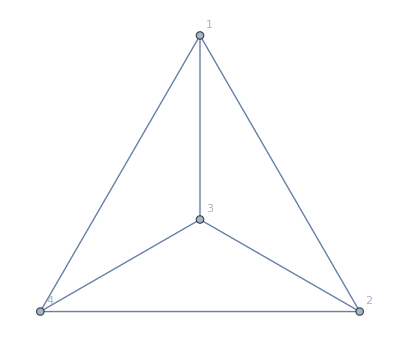
λ | Σ | α | α1 | α2 | β | β1 | β2 | γ | γ1 | γ2 | δ | δ1 | δ2 | ϵ | ϵ1 | ϵ2 | α+β+γ+δ+ϵ
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
{-Graphics-, | 1 | 2 | 3 | 4
1 | 1
0 | 0
1 | 0
1 | 0
1
2 | 0
1 | 1
0 | 0
1 | 0
1
3 | 0
1 | 0
1 | 1
0 | 0
1
4 | 0
1 | 0
1 | 0
1 | 1
0,1 | {0.333333,1/3,2
6}
2 | {0.333333,1/3,2
6}
3 | {0.333333,1/3,2
6}
4 | {0.333333,1/3,2
6},1/3,0.333333}

```mathematica
AlfaBetaPentagon33333[CompleteGraph[4],1,{1,2,3,4,1}]
```

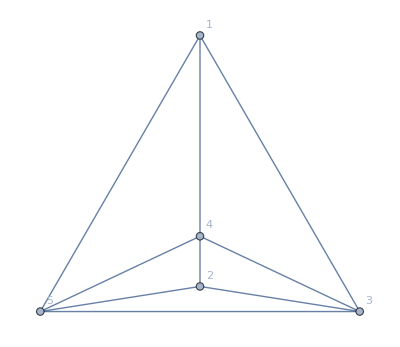
λ | Σ | α | α1 | α2 | β | β1 | β2 | γ | γ1 | γ2 | δ | δ1 | δ2 | ϵ | ϵ1 | ϵ2 | α+β+γ+δ+ϵ
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
{-Graphics-, | 1 | 2 | 3 | 4 | 5
1 | 1
0 | 1
0 | 0
1 | 0
1 | 0
1
2 | 1
0 | 1
0 | 0
1 | 0
1 | 0
1
3 | 0
1 | 0
1 | 1
0 | 0
1 | 0
1
4 | 0
1 | 0
1 | 0
1 | 1
0 | 0
1
5 | 0
1 | 0
1 | 0
1 | 0
1 | 1
0,1 | {0.666667,2/3,4
6}
2 | {0.666667,2/3,4
6}
3 | {0.25,1/4,2
8}
4 | {0.25,1/4,2
8}
5 | {0.25,1/4,2
8},7/18,0.388889}

```mathematica
AlfaBetaPentagon33333[EdgeDelete[CompleteGraph[5],1<->2],1,{1,2,3,4,5}]
```